## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PYK2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;

(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
(*Q10 = 2.5; Average factor for biological systems*)

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data_model.csv";

mainFolder = "fit_random";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PYK_Enzyme2/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

(adp^c+pep^c⇌atp^c+pyr^c)^PYK2

;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp,Null;pep,Null | 22000 | 20900.
23100. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | adp | 0.00017 | 0.0001615
0.0001785 | pep | 0.005 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | adp | 0.00012 | 0.000114
0.000126 | pep | 0.0005
r5p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | adp | 0.00012 | 0.000114
0.000126 | pep | 0.005
r5p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | 0.00082 | 0.000779
0.000861 |  | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | pep | 0.00019 | 0.0001805
0.0001995 | amp | 0.002 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | pep | 0.00013 | 0.0001235
0.0001365 | g6p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | pep | 0.0007 | 0.000665
0.000735 | r5p | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | pep | 0.00082 | 0.000779
0.000861 | pi | 0.001 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | adp | 0.00036 | 0.000342
0.000378 | pep | 0.0005 | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | pep | 1.58 | 1.501
1.659 |  |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | pep | 1.03 | 0.9785
1.0815 | amp | 0.002 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | pep | 1 | 0.95
1.05 | g6p | 0.001 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | pep | 0.99 | 0.9405
1.0395 | r5p | 0.001 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | pep | 2.1 | 1.995
2.205 | pi | 0.001 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05
1 | n | adp | 2 | 1.5
3 | pep | 0.0005 |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {10.^-5};
kmPriorities = {0,0,0};
s05Priorities = {1,0,0,0,0,0};
kcatPriorities = Null;
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities ={1,0,0,0,0,0};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(adp^c+pep^c⇌atp^c+pyr^c)^PYK2

;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
0.00001 | adp,Null;pep,Null | 22000 | 20900.
23100. | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | pep | 0.00082 | 0.000779
0.000861 |  | M | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | pep | 1.58 | 1.501
1.659 |  |  | 7.5 | 25 | hepes | 0.01 | mg2 | 0.01
cl | 0.02
cl | 0.05
k | 0.05

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
catalyticBranch={"E_PYK2[c] + adp[c] <=> E_PYK2[c]&adp",
				"E_PYK2[c]&adp + pep[c] <=> E_PYK2[c]&pep&adp",

				"E_PYK2[c] + pep[c] <=> E_PYK2[c]&pep",
				"E_PYK2[c]&pep + adp[c] <=> E_PYK2[c]&pep&adp",

				"E_PYK2[c]&pep&adp <=> E_PYK2[c]&pyr&atp",

				"E_PYK2[c]&pyr&atp <=> E_PYK2[c]&pyr + atp[c]",
				"E_PYK2[c]&pyr <=> E_PYK2[c] + pyr[c]",
				
				"E_PYK2[c]&pyr&atp <=> E_PYK2[c]&atp + pyr[c]",
				"E_PYK2[c]&atp <=> E_PYK2[c] + atp[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{m["amp","c"]},ActivationSites->4,Inhibitors->{},InhibitionSites->0];
(*enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{m["amp","c"], m["g6p","c"], m["r5p","c"]},ActivationSites->1,Inhibitors->{m["pi","c"]},InhibitionSites->1];*)
enzymeModel["Reactions"]
```

{((PYK2^c)_^+pep^c⇌(PYK2^c&pep^c)_^)^PYK21,((PYK2^c)_^+adp^c⇌(PYK2^c&adp^c)_^)^PYK22,((PYK2^c&atp^c)_^⇌(PYK2^c)_^+atp^c)^PYK23,((PYK2^c&pyr^c)_^⇌(PYK2^c)_^+pyr^c)^PYK24,((PYK2^c&pep^c)_^+adp^c⇌(PYK2^c&pep^c&adp^c)_^)^PYK25,((PYK2^c&adp^c)_^+pep^c⇌(PYK2^c&pep^c&adp^c)_^)^PYK26,((PYK2^c&pyr^c&atp^c)_^⇌(PYK2^c&atp^c)_^+pyr^c)^PYK27,((PYK2^c&pyr^c&atp^c)_^⇌(PYK2^c&pyr^c)_^+atp^c)^PYK28,((PYK2^c&pep^c&adp^c)_^⇌(PYK2^c&pyr^c&atp^c)_^)^PYK29,((PYK2^c)_^(amp^c)+pep^c⇌(PYK2^c&pep^c)_^(amp^c))^PYK21$3,((PYK2^c)_^(amp^c)+adp^c⇌(PYK2^c&adp^c)_^(amp^c))^PYK22$3,((PYK2^c&atp^c)_^(amp^c)⇌(PYK2^c)_^(amp^c)+atp^c)^PYK23$3,((PYK2^c&pyr^c)_^(amp^c)⇌(PYK2^c)_^(amp^c)+pyr^c)^PYK24$3,((PYK2^c&pep^c)_^(amp^c)+adp^c⇌(PYK2^c&pep^c&adp^c)_^(amp^c))^PYK25$3,((PYK2^c&adp^c)_^(amp^c)+pep^c⇌(PYK2^c&pep^c&adp^c)_^(amp^c))^PYK26$3,((PYK2^c&pyr^c&atp^c)_^(amp^c)⇌(PYK2^c&atp^c)_^(amp^c)+pyr^c)^PYK27$3,((PYK2^c&pyr^c&atp^c)_^(amp^c)⇌(PYK2^c&pyr^c)_^(amp^c)+atp^c)^PYK28$3,((PYK2^c&pep^c&adp^c)_^(amp^c)⇌(PYK2^c&pyr^c&atp^c)_^(amp^c))^PYK29$3,((PYK2^c)_^(amp^camp^c)+pep^c⇌(PYK2^c&pep^c)_^(amp^camp^c))^PYK21$7,((PYK2^c)_^(amp^camp^c)+adp^c⇌(PYK2^c&adp^c)_^(amp^camp^c))^PYK22$7,((PYK2^c&atp^c)_^(amp^camp^c)⇌(PYK2^c)_^(amp^camp^c)+atp^c)^PYK23$7,((PYK2^c&pyr^c)_^(amp^camp^c)⇌(PYK2^c)_^(amp^camp^c)+pyr^c)^PYK24$7,((PYK2^c&pep^c)_^(amp^camp^c)+adp^c⇌(PYK2^c&pep^c&adp^c)_^(amp^camp^c))^PYK25$7,((PYK2^c&adp^c)_^(amp^camp^c)+pep^c⇌(PYK2^c&pep^c&adp^c)_^(amp^camp^c))^PYK26$7,((PYK2^c&pyr^c&atp^c)_^(amp^camp^c)⇌(PYK2^c&atp^c)_^(amp^camp^c)+pyr^c)^PYK27$7,((PYK2^c&pyr^c&atp^c)_^(amp^camp^c)⇌(PYK2^c&pyr^c)_^(amp^camp^c)+atp^c)^PYK28$7,((PYK2^c&pep^c&adp^c)_^(amp^camp^c)⇌(PYK2^c&pyr^c&atp^c)_^(amp^camp^c))^PYK29$7,((PYK2^c)_^(amp^camp^camp^c)+pep^c⇌(PYK2^c&pep^c)_^(amp^camp^camp^c))^PYK21$8,((PYK2^c)_^(amp^camp^camp^c)+adp^c⇌(PYK2^c&adp^c)_^(amp^camp^camp^c))^PYK22$8,((PYK2^c&atp^c)_^(amp^camp^camp^c)⇌(PYK2^c)_^(amp^camp^camp^c)+atp^c)^PYK23$8,((PYK2^c&pyr^c)_^(amp^camp^camp^c)⇌(PYK2^c)_^(amp^camp^camp^c)+pyr^c)^PYK24$8,((PYK2^c&pep^c)_^(amp^camp^camp^c)+adp^c⇌(PYK2^c&pep^c&adp^c)_^(amp^camp^camp^c))^PYK25$8,((PYK2^c&adp^c)_^(amp^camp^camp^c)+pep^c⇌(PYK2^c&pep^c&adp^c)_^(amp^camp^camp^c))^PYK26$8,((PYK2^c&pyr^c&atp^c)_^(amp^camp^camp^c)⇌(PYK2^c&atp^c)_^(amp^camp^camp^c)+pyr^c)^PYK27$8,((PYK2^c&pyr^c&atp^c)_^(amp^camp^camp^c)⇌(PYK2^c&pyr^c)_^(amp^camp^camp^c)+atp^c)^PYK28$8,((PYK2^c&pep^c&adp^c)_^(amp^camp^camp^c)⇌(PYK2^c&pyr^c&atp^c)_^(amp^camp^camp^c))^PYK29$8,((PYK2^c)_^(amp^camp^camp^camp^c)+pep^c⇌(PYK2^c&pep^c)_^(amp^camp^camp^camp^c))^PYK21$10,((PYK2^c)_^(amp^camp^camp^camp^c)+adp^c⇌(PYK2^c&adp^c)_^(amp^camp^camp^camp^c))^PYK22$10,((PYK2^c&atp^c)_^(amp^camp^camp^camp^c)⇌(PYK2^c)_^(amp^camp^camp^camp^c)+atp^c)^PYK23$10,((PYK2^c&pyr^c)_^(amp^camp^camp^camp^c)⇌(PYK2^c)_^(amp^camp^camp^camp^c)+pyr^c)^PYK24$10,((PYK2^c&pep^c)_^(amp^camp^camp^camp^c)+adp^c⇌(PYK2^c&pep^c&adp^c)_^(amp^camp^camp^camp^c))^PYK25$10,((PYK2^c&adp^c)_^(amp^camp^camp^camp^c)+pep^c⇌(PYK2^c&pep^c&adp^c)_^(amp^camp^camp^camp^c))^PYK26$10,((PYK2^c&pyr^c&atp^c)_^(amp^camp^camp^camp^c)⇌(PYK2^c&atp^c)_^(amp^camp^camp^camp^c)+pyr^c)^PYK27$10,((PYK2^c&pyr^c&atp^c)_^(amp^camp^camp^camp^c)⇌(PYK2^c&pyr^c)_^(amp^camp^camp^camp^c)+atp^c)^PYK28$10,((PYK2^c&pep^c&adp^c)_^(amp^camp^camp^camp^c)⇌(PYK2^c&pyr^c&atp^c)_^(amp^camp^camp^camp^c))^PYK29$10,((PYK2^c)_^+amp^c⇌(PYK2^c)_^(amp^c))^PYK2_Activation_amp$11,((PYK2^c)_^(amp^c)+amp^c⇌(PYK2^c)_^(amp^camp^c))^PYK2_Activation_amp$12,((PYK2^c)_^(amp^camp^c)+amp^c⇌(PYK2^c)_^(amp^camp^camp^c))^PYK2_Activation_amp$14,((PYK2^c)_^(amp^camp^camp^c)+amp^c⇌(PYK2^c)_^(amp^camp^camp^camp^c))^PYK2_Activation_amp$15}

### Define all catalytic tracks

```mathematica
(*catalyticReactionsSet1={((PYK2^c)_^+pep^c⇌(PYK2^c&pep^c)_^)^PYK21,((PYK2^c&pep^c)_^+adp^c⇌(PYK2^c&pep^c&adp^c)_^)^PYK25,((PYK2^c&pep^c&adp^c)_^⇌(PYK2^c&pyr^c&atp^c)_^)^PYK29,((PYK2^c&pyr^c&atp^c)_^⇌(PYK2^c&atp^c)_^+pyr^c)^PYK27,((PYK2^c&atp^c)_^⇌(PYK2^c)_^+atp^c)^PYK23};*)
catalyticReactionsSet1={((PYK2^c)_^+adp^c⇌(PYK2^c&adp^c)_^)^PYK22,((PYK2^c&adp^c)_^+pep^c⇌(PYK2^c&pep^c&adp^c)_^)^PYK26,((PYK2^c&pep^c&adp^c)_^⇌(PYK2^c&pyr^c&atp^c)_^)^PYK29,Overscript[(PYK2^c&pyr^c&atp^c)_^⇌(PYK2^c&atp^c)_^+pyr^c, PYK27],Overscript[(PYK2^c&atp^c)_^⇌(PYK2^c)_^+atp^c, PYK23]};
(*catalyticReactionsSet3={((PYK2^c)_^+pep^c⇌(PYK2^c&pep^c)_^)^PYK21,((PYK2^c&pep^c)_^+adp^c⇌(PYK2^c&pep^c&adp^c)_^)^PYK25,((PYK2^c&pep^c&adp^c)_^⇌(PYK2^c&pyr^c&atp^c)_^)^PYK29,((PYK2^c&pyr^c&atp^c)_^⇌(PYK2^c&pyr^c)_^+atp^c)^PYK28,((PYK2^c&pyr^c)_^⇌(PYK2^c)_^+pyr^c)^PYK24};
catalyticReactionsSet4={((PYK2^c)_^+adp^c⇌(PYK2^c&adp^c)_^)^PYK22,((PYK2^c&adp^c)_^+pep^c⇌(PYK2^c&pep^c&adp^c)_^)^PYK26,((PYK2^c&pep^c&adp^c)_^⇌(PYK2^c&pyr^c&atp^c)_^)^PYK29,((PYK2^c&pyr^c&atp^c)_^⇌(PYK2^c&pyr^c)_^+atp^c)^PYK28,((PYK2^c&pyr^c)_^⇌(PYK2^c)_^+pyr^c)^PYK24};*)
(*catalyticReactionsSet3={((PYK2^c)_^(amp^c)+pep^c⇌(PYK2^c&pep^c)_^(amp^c))^PYK21$3,((PYK2^c&pep^c)_^(amp^c)+adp^c⇌(PYK2^c&pep^c&adp^c)_^(amp^c))^PYK25$3,((PYK2^c&pep^c&adp^c)_^(amp^c)⇌(PYK2^c&pyr^c&atp^c)_^(amp^c))^PYK29$3,((PYK2^c&pyr^c&atp^c)_^(amp^c)⇌(PYK2^c&atp^c)_^(amp^c)+pyr^c)^PYK27$3,((PYK2^c&atp^c)_^(amp^c)⇌(PYK2^c)_^(amp^c)+atp^c)^PYK23$3};*)
catalyticReactionsSet2={Overscript[(PYK2^c)_^(amp^c)+adp^c⇌(PYK2^c&adp^c)_^(amp^c), PYK22$3],Overscript[(PYK2^c&adp^c)_^(amp^c)+pep^c⇌(PYK2^c&pep^c&adp^c)_^(amp^c), PYK26$3],Overscript[(PYK2^c&pep^c&adp^c)_^(amp^c)⇌(PYK2^c&pyr^c&atp^c)_^(amp^c), PYK29$3],Overscript[(PYK2^c&pyr^c&atp^c)_^(amp^c)⇌(PYK2^c&atp^c)_^(amp^c)+pyr^c, PYK27$3],Overscript[(PYK2^c&atp^c)_^(amp^c)⇌(PYK2^c)_^(amp^c)+atp^c, PYK23$3]};
(*catalyticReactionsSet7={((PYK2^c)_^(amp^c)+pep^c⇌(PYK2^c&pep^c)_^(amp^c))^PYK21$3,((PYK2^c&pep^c)_^(amp^c)+adp^c⇌(PYK2^c&pep^c&adp^c)_^(amp^c))^PYK25$3,((PYK2^c&pep^c&adp^c)_^(amp^c)⇌(PYK2^c&pyr^c&atp^c)_^(amp^c))^PYK29$3,((PYK2^c&pyr^c&atp^c)_^(amp^c)⇌(PYK2^c&pyr^c)_^(amp^c)+atp^c)^PYK28$3,((PYK2^c&pyr^c)_^(amp^c)⇌(PYK2^c)_^(amp^c)+pyr^c)^PYK24$3};
catalyticReactionsSet8={((PYK2^c)_^(amp^c)+adp^c⇌(PYK2^c&adp^c)_^(amp^c))^PYK22$3,((PYK2^c&adp^c)_^(amp^c)+pep^c⇌(PYK2^c&pep^c&adp^c)_^(amp^c))^PYK26$3,((PYK2^c&pep^c&adp^c)_^(amp^c)⇌(PYK2^c&pyr^c&atp^c)_^(amp^c))^PYK29$3,((PYK2^c&pyr^c&atp^c)_^(amp^c)⇌(PYK2^c&pyr^c)_^(amp^c)+atp^c)^PYK28$3,((PYK2^c&pyr^c)_^(amp^c)⇌(PYK2^c)_^(amp^c)+pyr^c)^PYK24$3};*)
catalyticReactionsSetsList = {catalyticReactionsSet1, catalyticReactionsSet2(*, catalyticReactionsSet3, catalyticReactionsSet4 , catalyticReactionsSet5, catalyticReactionsSet6, catalyticReactionsSet7, catalyticReactionsSet8*)};
```

### Setup King-Altman Equations

```mathematica
MWCFlag=True;
nActiveSites=4;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{adp^c→1/10000000000,pep^c→1/10000000000}

{atp^c→1/10000000000,pyr^c→1/10000000000}

{adp^c→∞,pep^c→∞}

{atp^c→∞,pyr^c→∞}

1

2

```mathematica
Cases[2*pep^c+2, _metabolite]
```

{}

```mathematica
rateConstsSub
```

{k_PYK22^⟵→x<0>,k_PYK22^⟶→x<1>,k_PYK23^⟵→x<2>,k_PYK23^⟶→x<3>,k_PYK26^⟵→x<4>,k_PYK26^⟶→x<5>,k_PYK26$3^⟵→x<6>,k_PYK26$3^⟶→x<7>,k_PYK27^⟵→x<8>,k_PYK27^⟶→x<9>,k_PYK27$3^⟵→x<10>,k_PYK27$3^⟶→x<11>,k_PYK29^⟵→x<12>,k_PYK29^⟶→x<13>,k_PYK29$3^⟵→x<14>,k_PYK29$3^⟶→x<15>}

```mathematica
haldaneRatiosList
```

{(k_PYK22^⟶ k_PYK23^⟶ k_PYK26^⟶ k_PYK27^⟶ k_PYK29^⟶)/(k_PYK22^⟵ k_PYK23^⟵ k_PYK26^⟵ k_PYK27^⟵ k_PYK29^⟵),(k_PYK22^⟶ k_PYK23^⟶ k_PYK26$3^⟶ k_PYK27$3^⟶ k_PYK29$3^⟶)/(k_PYK22^⟵ k_PYK23^⟵ k_PYK26$3^⟵ k_PYK27$3^⟵ k_PYK29$3^⟵)}

## Semi-Automated Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
haldaneRelation["PYK2",catalyticReactionsSet1]
```

K_PYK2==(k_PYK22^⟶ k_PYK23^⟶ k_PYK26^⟶ k_PYK27^⟶ k_PYK29^⟶)/(k_PYK22^⟵ k_PYK23^⟵ k_PYK26^⟵ k_PYK27^⟵ k_PYK29^⟵)

```mathematica
haldaneRatiosList={haldaneRelation["PYK2",catalyticReactionsSet1][[2]]}
```

{(k_PYK22^⟶ k_PYK23^⟶ k_PYK26^⟶ k_PYK27^⟶ k_PYK29^⟶)/(k_PYK22^⟵ k_PYK23^⟵ k_PYK26^⟵ k_PYK27^⟵ k_PYK29^⟵)}

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

```mathematica
FilePrint@dataPathList
```

Priority	adp[c]	pyr[c]	amp[c]	atp[c]	pep[c]	param_PYK2_total	param_pH	param_Temp	FileFlag	Target_Data
0.00001	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/haldaneRatio_1.txt"	22000
0.00001	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/haldaneRatio_1.txt"	22000
0.00001	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/haldaneRatio_1.txt"	22000
0.00001	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/haldaneRatio_1.txt"	22000
0.00001	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/haldaneRatio_1.txt"	22000
0.00001	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/haldaneRatio_1.txt"	22000
0.00001	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/haldaneRatio_1.txt"	22000
0.00001	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/haldaneRatio_1.txt"	22000
0.00001	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/haldaneRatio_1.txt"	22000
0.00001	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/haldaneRatio_1.txt"	22000
0.00001	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/haldaneRatio_1.txt"	22000
1	0.01	0	0	0	0.000082	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.025628579593138075
1	0.01	0	0	0	0.00012996124178181137	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.05163853343956844
1	0.01	0	0	0	0.00020597468738378554	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.10130111024046975
1	0.01	0	0	0	0.0003264478798538678	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.18919738896403587
1	0.01	0	0	0	0.0005173850224737583	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.32571790233494585
1	0.01	0	0	0	0.00082	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.49999999999999994
1	0.01	0	0	0	0.0012996124178181136	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.6742820976650542
1	0.01	0	0	0	0.0020597468738378574	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.8108026110359643
1	0.01	0	0	0	0.0032644787985386782	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.8986988897595302
1	0.01	0	0	0	0.0051738502247375825	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.9483614665604315
1	0.01	0	0	0	0.0082	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.974371420406862
1	0.01	0	0.002	0	0.000018999999999999994	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.08535924209948725
1	0.01	0	0.002	0	0.00003011297065676116	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.13041095099167196
1	0.01	0	0.002	0	0.00004772584219868205	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.19419208651791064
1	0.01	0	0.002	0	0.0000756403624051644	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.2791533687626553
1	0.01	0	0.002	0	0.00011988189545123664	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.38359130603510383
1	0.01	0	0.002	0	0.00018999999999999996	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.4999999999999999
1	0.01	0	0.002	0	0.0003011297065676116	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.6164086939648961
1	0.01	0	0.002	0	0.0004772584219868205	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.7208466312373446
1	0.01	0	0.002	0	0.0007564036240516448	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.8058079134820895
1	0.01	0	0.002	0	0.0011988189545123664	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.8695890490083279
1	0.01	0	0.002	0	0.0018999999999999996	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.9146407579005127

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	adp[c]	pyr[c]	amp[c]	atp[c]	pep[c]	param_PYK2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0.01	0	0	0	0.00007991582443792786	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.015902831541024776
1	0.01	0	0	0	0.0001266580461215894	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.03556494714830801
1	0.01	0	0	0	0.00020073947506853268	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.07761969088660572
1	0.01	0	0	0	0.000318150627494335	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.16109665305159715
1	0.01	0	0	0	0.0005042347636930027	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.30469369271602054
1	0.01	0	0	0	0.0007991582443792786	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.5000000000000004
1	0.01	0	0	0	0.001266580461215894	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.6953063072839801
1	0.01	0	0	0	0.0020073947506853286	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.8389033469484035
1	0.01	0	0	0	0.0031815062749433495	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.9223803091133944
1	0.01	0	0	0	0.005042347636930028	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.9644350528516922
1	0.01	0	0	0	0.007991582443792786	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.9840971684589753
1	0.01	0	0.002	0	0.000017485798341057487	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.09605342551581417
1	0.01	0	0.002	0	0.000027713122755489852	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.14264505828441865
1	0.01	0	0.002	0	0.00004392233959701506	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.20666943168063215
1	0.01	0	0.002	0	0.00006961221702427425	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.28971959590501123
1	0.01	0	0.002	0	0.00011032792887389794	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.38974763580070587
1	0.01	0	0.002	0	0.00017485798341057484	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.49999999999999994
1	0.01	0	0.002	0	0.0002771312275548985	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.6102523641992939
1	0.01	0	0.002	0	0.0004392233959701506	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.7102804040949886
1	0.01	0	0.002	0	0.0006961221702427433	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.7933305683193678
1	0.01	0	0.002	0	0.0011032792887389795	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.8573549417155812
1	0.01	0	0.002	0	0.0017485798341057486	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.9039465744841857

### Parameter scan

```mathematica
Export["GAPDParameterScanArguments.mx",{paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList}, "MX"];

Export["GAPDParameterScanResults.mx",{allFittingDataList, dataPathList, fileList, fileListSub},"MX"];
```

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Set::partw: Part 1 of {} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	adp[c]	pyr[c]	amp[c]	atp[c]	pep[c]	param_PYK2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0.01	0	0	0	0.000082	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.025628579593138075
1	0.01	0	0	0	0.00012996124178181137	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.05163853343956844
1	0.01	0	0	0	0.00020597468738378554	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.10130111024046975
1	0.01	0	0	0	0.0003264478798538678	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.18919738896403587
1	0.01	0	0	0	0.0005173850224737583	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.32571790233494585
1	0.01	0	0	0	0.00082	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.49999999999999994
1	0.01	0	0	0	0.0012996124178181136	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.6742820976650542
1	0.01	0	0	0	0.0020597468738378574	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.8108026110359643
1	0.01	0	0	0	0.0032644787985386782	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.8986988897595302
1	0.01	0	0	0	0.0051738502247375825	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.9483614665604315
1	0.01	0	0	0	0.0082	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.974371420406862
1	0.01	0	0.002	0	0.000018999999999999994	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.08535924209948725
1	0.01	0	0.002	0	0.00003011297065676116	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.13041095099167196
1	0.01	0	0.002	0	0.00004772584219868205	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.19419208651791064
1	0.01	0	0.002	0	0.0000756403624051644	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.2791533687626553
1	0.01	0	0.002	0	0.00011988189545123664	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.38359130603510383
1	0.01	0	0.002	0	0.00018999999999999996	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.4999999999999999
1	0.01	0	0.002	0	0.0003011297065676116	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.6164086939648961
1	0.01	0	0.002	0	0.0004772584219868205	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.7208466312373446
1	0.01	0	0.002	0	0.0007564036240516448	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.8058079134820895
1	0.01	0	0.002	0	0.0011988189545123664	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.8695890490083279
1	0.01	0	0.002	0	0.0018999999999999996	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt"	0.9146407579005127

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	20
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	16
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/absRateFor.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/absRateRev.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_adp.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateRev_atp.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateRev_pyr.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	16
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/absRateFor.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/absRateRev.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_adp.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateFor_pep.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateRev_atp.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/PYK_Enzyme2/fit/input/relRateRev_pyr.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 2.01397467148
best_fit: 2.01490287301
best_fit: 2.02159408216
best_fit: 2.01399550305
best_fit: 2.01397457666
best_fit: 2.01397465304
best_fit: 2.01624932768
best_fit: 2.01397515179
best_fit: 2.01702319294
best_fit: 2.01423328984

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
filteredDataList[[All,1]]
```

{3.16782×10^9,5.32313×10^9,5.324×10^9,5.324×10^9,5.324×10^9,5.324×10^9,5.324×10^9,5.324×10^9,5.324×10^9,5.324×10^9}

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Residual | Residual^2 | Relative error | True value | Predicted Value
 |  |  |  |  |  | 
0.00001 | haldaneRatio_1 | 0.640863 | 0.410705 | 77.1368 | 22000 | 5029.91
0.00001 | haldaneRatio_1 | 0.640863 | 0.410705 | 77.1368 | 22000 | 5029.91
0.00001 | haldaneRatio_1 | 0.640863 | 0.410705 | 77.1368 | 22000 | 5029.91
0.00001 | haldaneRatio_1 | 0.640863 | 0.410705 | 77.1368 | 22000 | 5029.91
0.00001 | haldaneRatio_1 | 0.640863 | 0.410705 | 77.1368 | 22000 | 5029.91
0.00001 | haldaneRatio_1 | 0.640863 | 0.410705 | 77.1368 | 22000 | 5029.91
0.00001 | haldaneRatio_1 | 0.640863 | 0.410705 | 77.1368 | 22000 | 5029.91
0.00001 | haldaneRatio_1 | 0.640863 | 0.410705 | 77.1368 | 22000 | 5029.91
0.00001 | haldaneRatio_1 | 0.640863 | 0.410705 | 77.1368 | 22000 | 5029.91
0.00001 | haldaneRatio_1 | 0.640863 | 0.410705 | 77.1368 | 22000 | 5029.91
0.00001 | haldaneRatio_1 | 0.640863 | 0.410705 | 77.1368 | 22000 | 5029.91
1 | relRateFor_pep | 0.758527 | 0.575363 | 473.491 | 0.0256286 | 0.146978
1 | relRateFor_pep | 0.618461 | 0.382494 | 315.395 | 0.0516385 | 0.214504
1 | relRateFor_pep | 0.47449 | 0.225141 | 198.188 | 0.101301 | 0.302068
1 | relRateFor_pep | 0.332532 | 0.110577 | 115.046 | 0.189197 | 0.406862
1 | relRateFor_pep | 0.203895 | 0.0415731 | 59.9171 | 0.325718 | 0.520879
1 | relRateFor_pep | 0.10227 | 0.0104591 | 26.5522 | 0.5 | 0.632761
1 | relRateFor_pep | 0.0356466 | 0.00127068 | 8.55418 | 0.674282 | 0.731961
1 | relRateFor_pep | 0.000808581 | 6.53804×10^-7 | 0.186356 | 0.810803 | 0.812314
1 | relRateFor_pep | 0.0127169 | 0.000161719 | 2.88571 | 0.898699 | 0.872765
1 | relRateFor_pep | 0.0151899 | 0.000230733 | 3.43715 | 0.948361 | 0.915765
1 | relRateFor_pep | 0.0132256 | 0.000174917 | 2.99941 | 0.974371 | 0.945146
1 | relRateFor_pep | 0.347021 | 0.120424 | 55.0242 | 0.0853592 | 0.038391
1 | relRateFor_pep | 0.340729 | 0.116096 | 54.3678 | 0.130411 | 0.0595093
1 | relRateFor_pep | 0.328506 | 0.107916 | 53.0653 | 0.194192 | 0.0911435
1 | relRateFor_pep | 0.308673 | 0.0952789 | 50.8722 | 0.279153 | 0.137142
1 | relRateFor_pep | 0.280208 | 0.0785167 | 47.5444 | 0.383591 | 0.201215
1 | relRateFor_pep | 0.243631 | 0.0593559 | 42.9351 | 0.5 | 0.285325
1 | relRateFor_pep | 0.201557 | 0.0406253 | 37.1301 | 0.616409 | 0.387536
1 | relRateFor_pep | 0.158258 | 0.0250456 | 30.5388 | 0.720847 | 0.500708
1 | relRateFor_pep | 0.118198 | 0.0139709 | 23.8269 | 0.805808 | 0.613809
1 | relRateFor_pep | 0.0845045 | 0.007141 | 17.6819 | 0.869589 | 0.71583
1 | relRateFor_pep | 0.0583266 | 0.00340199 | 12.5674 | 0.914641 | 0.799694

### Simulated Data and Best Fit Data Plot

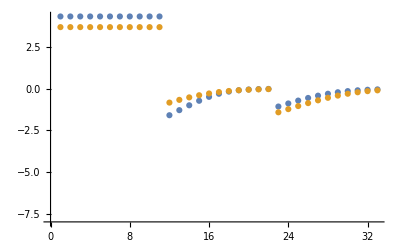

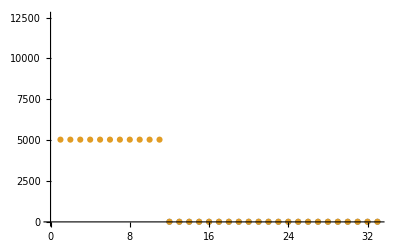

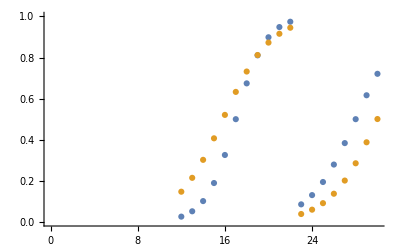

```mathematica
dataSet=1;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSet,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSet,3]]}, AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]], filteredDataList[[dataSet,3]]}, AxesOrigin->{0,-8}, PlotRange->{{0,30}, {0,1}}]
```

### Parameter Distribution

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

Transpose::nmtx: The first two levels of {Missing[]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

DistributionChart::ldata: Transpose[{}] is not a valid dataset or list of datasets.

General::stop: Further output of DistributionChart::ldata will be suppressed during this calculation.

DistributionChart[Transpose[{}],ChartElementFunction→HistogramDensity,PlotRange→{-7,10},ChartLegends→{k_PYK22^⟵,k_PYK22^⟶,k_PYK23^⟵,k_PYK23^⟶,k_PYK26^⟵,k_PYK26^⟶,k_PYK26$3^⟵,k_PYK26$3^⟶,k_PYK27^⟵,k_PYK27^⟶,k_PYK27$3^⟵,k_PYK27$3^⟶,k_PYK29^⟵,k_PYK29^⟶,k_PYK29$3^⟵,k_PYK29$3^⟶},ChartStyle→24]

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

Part::partw: Part 2 of {0} does not exist.

Table::iterb: Iterator {MASSef`Private`j,1,{0}⟦2⟧,2} does not have appropriate bounds.

Part::partw: Part 2 of {0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Table::iterb: Iterator {MASSef`Private`j,1,{0}⟦2⟧,2} does not have appropriate bounds.

Part::partw: Part 2 of {0} does not exist.

Table::iterb: Iterator {MASSef`Private`j,1,{0}⟦2⟧,2} does not have appropriate bounds.

DistributionChart::ldata: Log[Transpose[Transpose[Table[({}⟦All,2⟧⟦All,MASSef`Private`j+1⟧)/(Part[«3»]⟦All,MASSef`Private`j⟧),{MASSef`Private`j,1,{0}⟦2⟧,2}]]]]/Log[10] is not a valid dataset or list of datasets.

Table::iterb: Iterator {MASSef`Private`j,1,{0}⟦2⟧,2} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

DistributionChart::ldata: Log[Transpose[Transpose[Table[({}⟦All,2⟧⟦All,MASSef`Private`j+1⟧)/(Part[«3»]⟦All,MASSef`Private`j⟧),{MASSef`Private`j,1,{0}⟦2⟧,2}]]]]/Log[10] is not a valid dataset or list of datasets.

General::stop: Further output of DistributionChart::ldata will be suppressed during this calculation.

DistributionChart[Log[Transpose[Transpose[Table[({}⟦All,2⟧⟦All,MASSef`Private`j+1⟧)/({}⟦All,2⟧⟦All,MASSef`Private`j⟧),{MASSef`Private`j,1,{0}⟦2⟧,2}]]]]/Log[10],ChartElementFunction→HistogramDensity,ChartLegends→{PYK22,PYK23,PYK26,PYK26$3,PYK27,PYK27$3,PYK29,PYK29$3},ChartStyle→24]

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

Transpose::nmtx: The first two levels of {Missing[]} cannot be transposed.

DistributionChart::ldata: Transpose[{}] is not a valid dataset or list of datasets.

Transpose::nmtx: The first two levels of {Missing[]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

DistributionChart::ldata: Transpose[{}] is not a valid dataset or list of datasets.

General::stop: Further output of DistributionChart::ldata will be suppressed during this calculation.

DistributionChart[Transpose[{}],ChartLabels→{x<0>,x<1>,x<2>,x<3>,x<4>,x<5>,x<6>,x<7>,x<8>,x<9>,x<10>,x<11>,x<12>,x<13>,x<14>,x<15>},PlotRange→{-7,10},ChartLegends→{k_PYK22^⟵,k_PYK22^⟶,k_PYK23^⟵,k_PYK23^⟶,k_PYK26^⟵,k_PYK26^⟶,k_PYK26$3^⟵,k_PYK26$3^⟶,k_PYK27^⟵,k_PYK27^⟶,k_PYK27$3^⟵,k_PYK27$3^⟶,k_PYK29^⟵,k_PYK29^⟶,k_PYK29$3^⟵,k_PYK29$3^⟶},ChartStyle→24]

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

Transpose::nmtx: The first two levels of {Missing[]} cannot be transposed.

DistributionChart::ldata: Transpose[{}] is not a valid dataset or list of datasets.

Transpose::nmtx: The first two levels of {Missing[]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

DistributionChart::ldata: Transpose[{}] is not a valid dataset or list of datasets.

General::stop: Further output of DistributionChart::ldata will be suppressed during this calculation.

DistributionChart[Transpose[{}],ChartElementFunction→HistogramDensity,ChartLegends→{relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep,relRateFor_pep},ChartStyle→24]

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

Part::partw: Part 1 of {} does not exist.

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 3 of {}⟦1⟧ does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

data value | predicted value | error in %
{}⟦1⟧⟦3⟧ | 1 | (100 Abs[-1+{}⟦1⟧⟦3⟧])/({}⟦1⟧⟦3⟧)

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

Part::partw: Part 1 of {} does not exist.

data value | predicted value | error in %
22000 | {}⟦1⟧ | 1/220 Abs[22000-{}⟦1⟧]